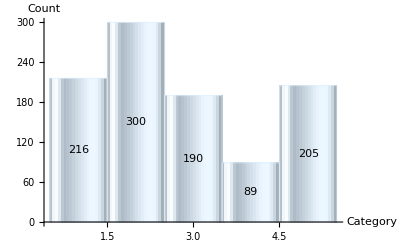

```mathematica
weights={200,300,200,100,200};
categories=Range[1,Length[weights]];
dist=EmpiricalDistribution[weights->categories];
data=RandomVariate[dist,1000];
Histogram[data,LabelingFunction-> Center,ChartElementFunction->"GlassRectangle",ChartStyle->LightBlue,AxesLabel->{"Category","Count"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/sampling_from_discrete_distribution.png"}],%,ImageResolution->300]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\sampling_from_discrete_distribution.png

```mathematica
doorsWithPrize=RandomChoice[{1,2,3},1000000];
firstChoice=RandomChoice[{1,2,3},Length[doorsWithPrize]];
doorsWithoutPrize=MapThread[RandomChoice[Complement[{1,2,3},{#1,#2}]]&,{doorsWithPrize,firstChoice}];
secondChoice=MapThread[RandomChoice[Complement[{1,2,3},{#1,#2}]]&,{doorsWithoutPrize,firstChoice}];
ProbabilityWinningPrize[choice_]:=Apply[Plus,MapThread[Boole[#1==#2]&,{doorsWithPrize,choice}]]/Length[doorsWithPrize]//N;
Print["Probability of winning by staying with your first choice = ",ProbabilityWinningPrize[firstChoice]];
Print["Probability of winning by choosing the remaining door = ",ProbabilityWinningPrize[secondChoice]];
```

Probability of winning by staying with your first choice = 0.333221

Probability of winning by choosing the remaining door = 0.666779